```mathematica
P={-8,11};Q={7,4};
```

```mathematica
V=Q-P
```

{15,-7}

```mathematica
ArrowPlots6=Graphics[{Arrowheads[.07],Thickness[.010],Black,Arrow[{{0,0},P}],Black,Arrow[{{0,0},Q}],Red,Arrow[{P,Q}],Blue,Arrow[{{0,0},V}]}];
```

```mathematica
TxtPlots6=Graphics[{Black,Text["P",{-5,5}],Text["Q",{4.5,1}],Text["PQ",{0,9}],Text["V",{10,-3}]}];
```

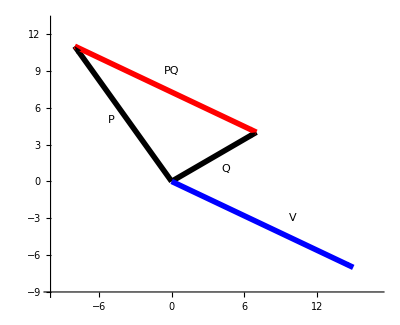

```mathematica
Show[ArrowPlots6,TxtPlots6,PlotRange-> {{-10,17},{-9,13}},Axes-> True,AxesOrigin-> {-10,-9}]
```

```mathematica
o={0,0}
```

{0,0}

```mathematica
p={-8,11}
```

{-8,11}

```mathematica
q={7,4}
```

{7,4}

```mathematica
vectorGraphics[p_]:=Graphics[{Arrowheads[.07],Thickness[.01],Black,Arrow[{{0,0},p}]}]
```

```mathematica
g=vectorGraphics@p;
```

```mathematica
g2=vectorGraphics@q;
```

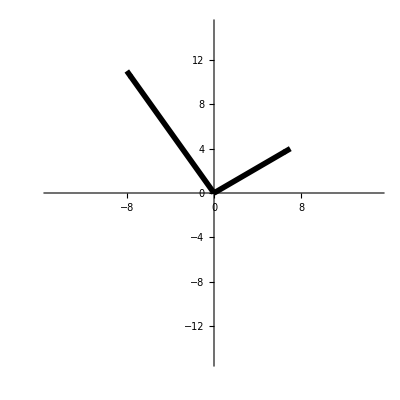

```mathematica
Show[g,g2,PlotRange-> {{-15,15},{-15,15}},Axes-> True,AxesOrigin-> {0,0}]
```